# FeynCalc gg -> B Bbar

```mathematica
Quit[]
```

### Installation

```mathematica
(*Import["https://raw.githubusercontent.com/FeynCalc/feyncalc/master/install.m"]
InstallFeynCalc[]*)
```

## qqbar example

```mathematica
description="Gl Gl -> Q Qbar, QCD, matrix element squared, tree";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
LaunchKernels[4];

$ParallelizeFeynCalc=True;
FCCheckVersion[10,2,0];
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

Join::incpt: Incompatible elements in Join[«1»] cannot be joined.

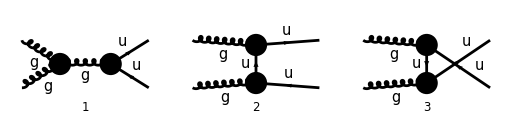

```mathematica
FCAttachTypesettingRule[p1,{SubscriptBox,p,1}]
FCAttachTypesettingRule[p2,{SubscriptBox,p,2}]
FCAttachTypesettingRule[q1,{SubscriptBox,q,1}]
FCAttachTypesettingRule[q2,{SubscriptBox,q,2}]

diags=InsertFields[CreateTopologies[0,2->2],{V[5],V[5]}->{F[3,{1}],-F[3,{1}]},InsertionLevel->{Classes},Model->"SMQCD"];

Paint[diags,ColumnsXRows->{4,1},Numbering->Simple,SheetHeader->None,ImageSize->128 {4,1}];
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},OutgoingMomenta->{q1,q2},UndoChiralSplittings->True,ChangeDimension->D,TransversePolarizationVectors->{p1,p2},List->True,SMP->True,Contract->True,DropSumOver->True];
```

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-q1,-q2,0,0,SMP["m_u"],SMP["m_u"]];
```

```mathematica
ampSquared[0]=SquareAmplitude[amp[0],ComplexConjugate[amp[0]],Real->True];
```

```mathematica
AbsoluteTiming[ampSquared[1]=FeynAmpDenominatorExplicit[ampSquared[0],FCParallelize->True]//SUNSimplify[#,FCParallelize->True]&;]
```

{0.119247,Null}

```mathematica
AbsoluteTiming[ampSquared[2]=ampSquared[1]//DoPolarizationSums[#,p1,p2,FCParallelize->True,ExtraFactor->1/2]&//DoPolarizationSums[#,p2,p1,FCParallelize->True,ExtraFactor->1/2]&;]
```

{0.591337,Null}

```mathematica
AbsoluteTiming[ampSquared[3]=ampSquared[2]//FermionSpinSum[#,FCParallelize->True]&//DiracSimplify[#,FCParallelize->True]&;]
AbsoluteTiming[ampSquared[4]=1/((SUNN^2-1)^2) ampSquared[3]//TrickMandelstam[#,{s,t,u,2 SMP["m_u"]^2},FCParallelize->True]&;]
```

{1.90576,Null}

{0.138986,Null}

```mathematica
ampSquared[5]=Collect2[ampSquared[4]//Total,CA,CF,D,Factoring->Function[{x},TrickMandelstam[x,{s,t,u,2 SMP["m_u"]^2}]]]
```

(D^2 C_A C_F^2 g_s^4 (-2 t m_u^2+2 m_u^4-2 u m_u^2+t^2+u^2))/(2 (1-N^2)^2 (u-m_u^2) (t-m_u^2))-(D C_A^2 C_F g_s^4 (-2 t m_u^2+2 m_u^4-2 u m_u^2+t^2+u^2))/((1-N^2)^2 s^2)-(2 D C_A C_F^2 g_s^4 (-2 t m_u^2+2 m_u^4-2 u m_u^2+t^2+u^2))/((1-N^2)^2 (u-m_u^2) (t-m_u^2))+(2 C_A^2 C_F g_s^4 (-t^3 m_u^2+2 t^2 m_u^4-3 t^2 u m_u^2-3 t u^2 m_u^2-4 t m_u^6+8 t u m_u^4-u^3 m_u^2+2 u^2 m_u^4+2 m_u^8-4 u m_u^6+2 t^3 u-2 t^2 u^2+2 t u^3))/((1-N^2)^2 s^2 (u-m_u^2) (t-m_u^2))+1/((1-N^2)^2 s^2 (u-m_u^2)^2 (t-m_u^2)^2)2 C_A C_F^2 g_s^4 (-t^5 m_u^2+7 t^4 m_u^4-11 t^4 u m_u^2-20 t^3 u^2 m_u^2-18 t^3 m_u^6+48 t^3 u m_u^4-20 t^2 u^3 m_u^2+58 t^2 u^2 m_u^4+16 t^2 m_u^8-78 t^2 u m_u^6-11 t u^4 m_u^2+48 t u^3 m_u^4-78 t u^2 m_u^6+56 t u m_u^8-u^5 m_u^2+7 u^4 m_u^4-18 u^3 m_u^6+16 u^2 m_u^8-8 m_u^12+t^5 u+6 t^3 u^3+t u^5)-(D^2 C_F g_s^4)/(2 (1-N^2)^2)+(3 D C_F g_s^4)/((1-N^2)^2)-(2 C_F g_s^4 (-2 t^3 m_u^2+9 t^2 m_u^4-18 t^2 u m_u^2-18 t u^2 m_u^2-12 t m_u^6+38 t u m_u^4-2 u^3 m_u^2+9 u^2 m_u^4-12 u m_u^6+3 t^3 u+2 t^2 u^2+3 t u^3))/((1-N^2)^2 s^2 (u-m_u^2) (t-m_u^2))

### Non-vanishing masses in 4 dimensions and 3 numbers of color

```mathematica
ampSquaredSUNN3[0]=TrickMandelstam[SUNSimplify[ampSquared[5]/. D->4,SUNNToCACF->False]/. SUNN->3,{s,t,u,2 SMP["m_u"]^2}]
```

1/(24 s^2 (u-m_u^2)^2 (t-m_u^2)^2)g_s^4 (4 s t^4 m_u^2+30 s t^3 u m_u^2-6 s t^2 u^2 m_u^2+20 s t^2 m_u^6+30 s t u^3 m_u^2+92 s t u m_u^6+4 s u^4 m_u^2+20 s u^2 m_u^6-66 s m_u^10+19 t^4 m_u^4+100 t^3 u m_u^4+68 t^2 u^2 m_u^4-27 t^2 m_u^8+100 t u^3 m_u^4+40 t u m_u^8+19 u^4 m_u^4-27 u^2 m_u^8-50 m_u^12+4 t^5 u-t^4 u^2+8 t^3 u^3-t^2 u^4+4 t u^5)

### Massless

```mathematica
ampSquaredMassless[0]=Collect2[ampSquared[5]//ReplaceAll[#,{SMP["m_u"]->0}]&,D,CA,CF,Factoring->Function[{x},TrickMandelstam[x,{s,t,u,2 SMP["m_u"]^2}]]]
```

(D^2 C_A C_F^2 g_s^4 (t^2+u^2))/(2 (1-N^2)^2 t u)-(D C_A^2 C_F g_s^4 (t^2+u^2))/((1-N^2)^2 s^2)-(2 D C_A C_F^2 g_s^4 (t^2+u^2))/((1-N^2)^2 t u)+(4 C_A^2 C_F g_s^4 (t^2-t u+u^2))/((1-N^2)^2 s^2)+(2 C_A C_F^2 g_s^4 (t^4+6 t^2 u^2+u^4))/((1-N^2)^2 s^2 t u)-(D^2 C_F g_s^4)/(2 (1-N^2)^2)+(3 D C_F g_s^4)/((1-N^2)^2)-(2 C_F g_s^4 (3 t^2+2 t u+3 u^2))/((1-N^2)^2 s^2)

```mathematica
ampSquaredMasslessSUNN3[0]=TrickMandelstam[SUNSimplify[ampSquaredMassless[0]/. D->4,SUNNToCACF->False]/. SUNN->3,{s,t,u,0}]
```

(g_s^4 (t^2+u^2) (4 t^2-t u+4 u^2))/(24 s^2 t u)

```mathematica
knownResults={(1/6) SMP["g_s"]^4 (t^2+u^2)/(t u)-(3/8) SMP["g_s"]^4 (t^2+u^2)/(s^2)};

FCCompareResults[{ampSquaredMasslessSUNN3[0]},{knownResults},Factoring->Function[x,Simplify[TrickMandelstam[x,{s,t,u,0}]]]];
```

Check of the results: The results agree.

## Without Color Trace

```mathematica
Quit[]
```

```mathematica
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
LaunchKernels[4];

$ParallelizeFeynCalc=True;
FCCheckVersion[10,2,0];
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

Join::incpt: Incompatible elements in Join[«1»] cannot be joined.

```mathematica
FCAttachTypesettingRule[p1,{SubscriptBox,p,1}]
FCAttachTypesettingRule[p2,{SubscriptBox,p,2}]
FCAttachTypesettingRule[q1,{SubscriptBox,q,1}]
FCAttachTypesettingRule[q2,{SubscriptBox,q,2}]

diags=InsertFields[CreateTopologies[0,2->2],{V[5],V[5]}->{F[3,{1}],-F[3,{1}]},InsertionLevel->{Classes},Model->"SMQCD"];

Paint[diags,ColumnsXRows->{4,1},Numbering->Simple,SheetHeader->None,ImageSize->128 {4,1}];
```

-Graphics-

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},OutgoingMomenta->{q1,q2},UndoChiralSplittings->True,ChangeDimension->D,TransversePolarizationVectors->{p1,p2},List->True,SMP->True,Contract->True,DropSumOver->True];

FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-q1,-q2,0,0,SMP["m_u"],SMP["m_u"]];
```

```mathematica
ampSquared[0]=SquareAmplitude[amp[0],ComplexConjugate[amp[0]],Real->True];
```

```mathematica
ampSquared[1]=FeynAmpDenominatorExplicit[ampSquared[0]];

ampSquared[2]=ampSquared[1]//DoPolarizationSums[#,p1,p2,ExtraFactor->1/2]&//DoPolarizationSums[#,p2,p1,ExtraFactor->1/2]&;

ampSquared[3]=ampSquared[2]//FermionSpinSum//DiracSimplify;

ampSquared[4]=TrickMandelstam[1/((SUNN^2-1)^2)ampSquared[3],{s,t,u,2 SMP["m_u"]^2}];

ampSquaredWithOpenColor=Simplify[Total[ampSquared[4]]/. D->4/. SUNN->3]
```

1/(128 s^2)g_s^4 (-(8 ⅈ T_Col3Col5^Glu2 T_Col5Col4^Glu1 (m_u^2 (2 s (t+u)+t^2+4 t u+u^2)-2 m_u^4 (s+t+2 u)+2 m_u^6-2 t u (s+t)) T_Col4Col3^($AL($12)) f^(Glu1Glu2$AL($12)))/(u-m_u^2)+(8 ⅈ T_Col3Col5^Glu1 T_Col5Col4^Glu2 (m_u^2 (2 s (t+u)+t^2+4 t u+u^2)-2 m_u^4 (s+2 t+u)+2 m_u^6-2 t u (s+u)) T_Col4Col3^($AL($12)) f^(Glu1Glu2$AL($12)))/(t-m_u^2)+(8 T_Col3Col5^Glu2 T_Col5Col4^Glu1 (m_u^4 (2 s^2-9 t^2-38 t u-9 u^2)+2 m_u^2 (t+u) (-s^2+t^2+8 t u+u^2)+12 m_u^6 (t+u)-t u (-2 s^2+3 t^2+2 t u+3 u^2)) T_($AL($13)Col3)^Glu1 T_(Col4$AL($13))^Glu2)/((m_u^2-u) (t-m_u^2))-(4 (-m_u^4 (3 t^2+24 t u+5 u^2)+m_u^2 (t^3+13 t^2 u+9 t u^2+u^3)+2 m_u^6 (t+3 u)+4 m_u^8-t u (3 t^2+u^2)) T_Col3Col5^Glu1 T_Col5Col4^Glu2 T_($AL($13)Col3)^Glu1 T_(Col4$AL($13))^Glu2)/((t-m_u^2)^2)-(4 (-m_u^4 (5 t^2+24 t u+3 u^2)+m_u^2 (t^3+9 t^2 u+13 t u^2+u^3)+2 m_u^6 (3 t+u)+4 m_u^8-t u (t^2+3 u^2)) T_Col3Col5^Glu2 T_Col5Col4^Glu1 T_($AL($14)Col3)^Glu2 T_(Col4$AL($14))^Glu1)/((u-m_u^2)^2)+8 (u-m_u^2) (t-m_u^2) T_Col3Col4^Glu5 f^Glu1Glu2Glu5 T_Col4Col3^($AL($12)) f^(Glu1Glu2$AL($12)))

## Final Expression (cross section)

```mathematica
Quit[]
```

```mathematica
(*Subscript[T, Col3Col5]^Glu2 Subscript[T, Col5Col4]^Glu1 Subscript[T, Col4Col3]^($AL($12)) f^(Glu1Glu2$AL($12))*)
TTTf1[TR_,dR_]:=-12 I TR;
(*Subscript[T, Col3Col5]^Glu1 Subscript[T, Col5Col4]^Glu2 Subscript[T, Col4Col3]^($AL($12)) f^(Glu1Glu2$AL($12))*)
TTTf2[TR_,dR_]:=12 I TR;
(*Subscript[T, Col3Col5]^Glu2 Subscript[T, Col5Col4]^Glu1 Subscript[T, $AL($13)Col3]^Glu1 Subscript[T, Col4$AL($13)]^Glu2*)
TTTT1[TR_,dR_]:= 64 TR^2/dR-12TR;
(*Subscript[T, Col3Col5]^Glu1 Subscript[T, Col5Col4]^Glu2 Subscript[T, $AL($13)Col3]^Glu1 Subscript[T, Col4$AL($13)]^Glu2*)
TTTT2[TR_,dR_]:= 64 TR^2/dR;
(*Subscript[T, Col3Col5]^Glu2 Subscript[T, Col5Col4]^Glu1 Subscript[T, $AL($14)Col3]^Glu2 Subscript[T, Col4$AL($14)]^Glu1*)
TTTT3[TR_,dR_]:= 64 TR^2/dR;
(* Subscript[T, Col3Col4]^Glu5 f^Glu1Glu2Glu5 Subscript[T, Col4Col3]^($AL($12)) f^(Glu1Glu2$AL($12))*)
TfTf[TR_,dR_]:= 24 TR;
```

```mathematica
ampSquared[TR_,dR_]:=(1/(128 s^2))Subscript[g, s]^4 (-1/(u-m^2)8 I  (m^2 (2 s (t+u)+t^2+4 t u+u^2)-2 m^4 (s+t+2 u)+2 m^6-2 t u (s+t)) TTTf1[TR,dR]+1/(t-m^2)8 I  (m^2 (2 s (t+u)+t^2+4 t u+u^2)-2 m^4 (s+2 t+u)+2 m^6-2 t u (s+u)) TTTf2[TR,dR]+1/((m^2-u) (t-m^2))8  (m^4 (2 s^2-9 t^2-38 t u-9 u^2)+2 m^2 (t+u) (-s^2+t^2+8 t u+u^2)+12 m^6 (t+u)-t u (-2 s^2+3 t^2+2 t u+3 u^2)) TTTT1[TR,dR]-1/((t-m^2)^2)4 (-m^4 (3 t^2+24 t u+5 u^2)+m^2 (t^3+13 t^2 u+9 t u^2+u^3)+2 m^6 (t+3 u)+4 m^8-t u (3 t^2+u^2)) TTTT2[TR,dR]-1/((u-m^2)^2)4 (-m^4 (5 t^2+24 t u+3 u^2)+m^2 (t^3+9 t^2 u+13 t u^2+u^3)+2 m^6 (3 t+u)+4 m^8-t u (t^2+3 u^2)) TTTT3[TR,dR]+8 (u-m^2) (t-m^2) TfTf[TR,dR]);
```

### Example: SM quarks

```mathematica
argument=Simplify[ampSquared[1/2,3]/. u->2 m^2-s-t]
```

-1/(24 s^2 (m^2-t)^2 (-m^2+s+t)^2)g_s^4 (18 m^12-18 m^10 (s+6 t)+m^8 (35 s^2+126 s t+270 t^2)-4 m^6 (9 s^3+35 s^2 t+81 s t^2+90 t^3)+m^4 (21 s^4+88 s^3 t+246 s^2 t^2+396 s t^3+270 t^4)-2 m^2 (2 s^5+13 s^4 t+52 s^3 t^2+106 s^2 t^3+117 s t^4+54 t^5)+t (4 s^5+21 s^4 t+52 s^3 t^2+71 s^2 t^3+54 s t^4+18 t^5))

```mathematica
lambda[s_,x_,y_]:=s^2+x^2+y^2-2 s x-2 s y-2 x y;
tMin=(2m^2-s-Sqrt[lambda[s,m^2,m^2]])/2;
tMax=(2 m^2-s+Sqrt[lambda[s,m^2,m^2]])/2;
```

```mathematica
result=Integrate[argument/(16 Pi s^2),{t,tMin,tMax},Assumptions->s>(2m)^2];
```

```mathematica
FullSimplify[result/.Sqrt[1-4m^2/s]->beta/.s-4m^2->beta^2*s/.Subscript[g, s]^4->16 Pi^2 α^2,Assumptions->beta>0&&s>0]
```

(π α^2 (8 tanh^-1(beta) (m^4+4 m^2 s+s^2)-beta s (31 m^2+7 s)))/(12 s^3)

### General analytic expression

```mathematica
argument=Simplify[ampSquared[TR,DR]/. u->2 m^2-s-t]
result=Integrate[argument/(16 Pi s^2),{t,tMin,tMax},Assumptions->s>(2m)^2];
FullSimplify[result/.Sqrt[1-4m^2/s]->beta/.s-4m^2->beta^2*s/.Subscript[g, s]^4->16 Pi^2 α^2,Assumptions->beta>0&&s>0]
```

-(TR g_s^4 (2 m^8-8 m^6 t+m^4 (3 s^2+4 s t+12 t^2)-m^2 (s^3+2 s^2 t+8 s t^2+8 t^3)+t (s^3+3 s^2 t+4 s t^2+2 t^3)) (3 DR (m^2-t) (m^2-s-t)+8 s^2 TR))/(4 DR s^2 (m^2-t)^2 (-m^2+s+t)^2)

-1/(2 DR s^3)π α^2 TR (beta s (DR (5 m^2+s)+8 TR (4 m^2+s))-8 tanh^-1(beta) (3 DR m^4+2 TR (-8 m^4+4 m^2 s+s^2)))

```mathematica
N[-(1/(2 DR s^3))π α^2 TR (beta s (DR (5 m^2+s)+8 TR (4 m^2+s))-8 ArcTanh[beta] (3 DR m^4+2 TR (-8 m^4+4 m^2 s+s^2)))/.beta->Sqrt[1-4m^2/s]/.m->0.0022/.s->7000^2/.α->0.118/.DR->3/.TR->1/2]
```

8.3903×10^-9

### Numerical examples

```mathematica
rep={"3","6","8",
"10","15","15'",
"21","24","27",
"42"};
dim={3,6,8,
10,15,15,
21,24,27,
42};
dynkin={1/2,5/2,3,
15/2,10,35/2,
35,25,27,
119/2};
```

```mathematica
For[i=1,i<=Length[rep],i++,
integral=Integrate[
Simplify[ampSquared[dynkin[[i]],dim[[i]]]/. u->2 m^2-s-t]/(16 Pi s^2),{t,tMin,tMax},Assumptions->s>(2m)^2
];
res=FullSimplify[integral/.Sqrt[1-4m^2/s]->beta/.s-4m^2->beta^2*s/.Subscript[g, s]^4->16 Pi^2 α^2,Assumptions->beta>0&&s>0];
Print["Irrep"rep[[i]]];
Print[res];
Print[N[res/.beta->Sqrt[1-4m^2/s]/.m->5000/.s->100000^2/.α->0.06]];
]
```

3 Irrep

(π α^2 (8 tanh^-1(beta) (m^4+4 m^2 s+s^2)-beta s (31 m^2+7 s)))/(12 s^3)

1.61572×10^-12

6 Irrep

-(5 π α^2 (beta s (55 m^2+13 s)+4 tanh^-1(beta) (22 m^4-20 m^2 s-5 s^2)))/(12 s^3)

2.23319×10^-11

8 Irrep

-(3 π α^2 (beta s (17 m^2+4 s)-6 tanh^-1(beta) (-4 m^4+4 m^2 s+s^2)))/(2 s^3)

2.39476×10^-11

10 Irrep

-(15 π α^2 (beta s (29 m^2+7 s)-12 tanh^-1(beta) (-6 m^4+4 m^2 s+s^2)))/(4 s^3)

1.24009×10^-10

15 Irrep

-(5 π α^2 (beta s (79 m^2+19 s)+8 tanh^-1(beta) (23 m^4-16 m^2 s-4 s^2)))/(3 s^3)

1.46341×10^-10

15' Irrep

-(35 π α^2 (beta s (127 m^2+31 s)+8 tanh^-1(beta) (47 m^4-28 m^2 s-7 s^2)))/(12 s^3)

4.55643×10^-10

21 Irrep

-(35 π α^2 (beta s (175 m^2+43 s)+8 tanh^-1(beta) (71 m^4-40 m^2 s-10 s^2)))/(6 s^3)

1.31038×10^-9

24 Irrep

-(25 π α^2 (beta s (115 m^2+28 s)+tanh^-1(beta) (328 m^4-200 m^2 s-50 s^2)))/(6 s^3)

5.79652×10^-10

27 Irrep

-(27 π α^2 (beta s (37 m^2+9 s)+8 tanh^-1(beta) (13 m^4-8 m^2 s-2 s^2)))/(2 s^3)

6.00368×10^-10

42 Irrep

-(119 π α^2 (beta s (151 m^2+37 s)+4 tanh^-1(beta) (118 m^4-68 m^2 s-17 s^2)))/(12 s^3)

1.88841×10^-9